## Probability of single resistance for the EG model with constant birth and death rates

### Input

```mathematica
ClearAll["Global`*"]
```

```mathematica
bS=0.5;
bA=0.8;
bB=0.9;
bD=1.0;
dS=0.1 ;
dA=0.1;
dB=0.1;
dD=0.1;
μA= 1 10^-6;
μB= 1 10^-4;
rS = bS(1-μA-μB)-dS;
rA = bA(1 - μB) - dA;
rB = bB(1 - μA) - dB;
rD = bD - dD;
n0 = 10^4;
```

### Single resistance

```mathematica
PhiASingle[T_]:=-n0 bS μA rA(1/(bA rS-bA rS μB)(ⅇ^(rS T) Hypergeometric2F1[1,rS/rA,(rA+rS)/rA,dA/(bA-bA μB)]-Hypergeometric2F1[1,rS/rA,(rA+rS)/rA,(dA ⅇ^(-rA T))/(bA-bA μB)]));
PhiBSingle[T_]:=-n0 bS μB rB(1/(bB rS-bB rS μA)(ⅇ^(rS T) Hypergeometric2F1[1,rS/rB,(rB+rS)/rB,dB/(bB-bB μA)]-Hypergeometric2F1[1,rS/rB,(rB+rS)/rB,(dB ⅇ^(-rB T))/(bB-bB μA)]));
PRSingle[T_]:=1-Exp[PhiASingle[T]+PhiBSingle[T]];
```

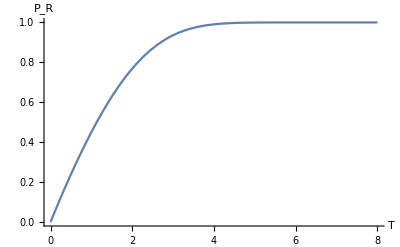

```mathematica
Plot[PRSingle[T],{T,0,8},PlotRange->All,AxesLabel->{"T","P_R"}]
```

### Double resistance

```mathematica
PhiADouble[T_]:=n0 bA μB rD((bS μA)/(rS - rA))(1/(bD rA)(ⅇ^(rA T) Hypergeometric2F1[1,rA/rD,(rA+rD)/rD,dD/bD]-Hypergeometric2F1[1,rA/rD,(rA+rD)/rD,(dD ⅇ^(-rD T))/bD]));
PhiBDouble[T_]:=n0 bB μA rD((bS μB)/(rS - rB))(1/(bD rB)(ⅇ^(rB T) Hypergeometric2F1[1,rB/rD,(rB+rD)/rD,dD/bD]-Hypergeometric2F1[1,rB/rD,(rB+rD)/rD,(dD ⅇ^(-rD T))/bD]));
PhiSDouble[T_]:=-n0 rD (bA μB ((bS μA)/(rS - rA)) + bB μA ((bS μB)/(rS - rB)))(1/(bD rS)(ⅇ^(rS T) Hypergeometric2F1[1,rS/rD,(rD+rS)/rD,dD/bD]-Hypergeometric2F1[1,rS/rD,(rD+rS)/rD,(dD ⅇ^(-rD T))/bD]));
PRDouble[T_]:=1-Exp[PhiADouble[T]+PhiBDouble[T] + PhiSDouble[T]];
```

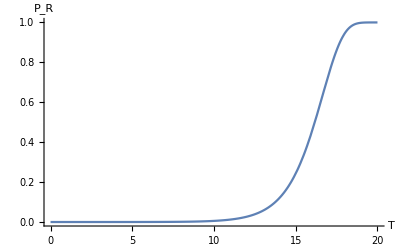

```mathematica
Plot[PRDouble[T],{T,0,20},PlotRange->All,AxesLabel->{"T","P_R"}]
```

## Probability of single and double resistance for the linear model with time-dependent birth and death rates

```mathematica
<<MaTeX`
```

### Input

```mathematica
ClearAll["Global`*"]
```

#### Constant rates

```mathematica
bS[t_]:=1.1;
bA[t_]:=1.0;
bB[t_]:=1.3;
bD[t_]:=1.4;
dS[t_]:=0.1;
dA[t_]:=0.1;
dB[t_]:=0.1 ;
dD[t_]:=0.1;
μA= 1 10^-4;
μB= 1 10^-4;
n0 = 5 10^5;
tmax=100;
```

#### Sinusoidal rates

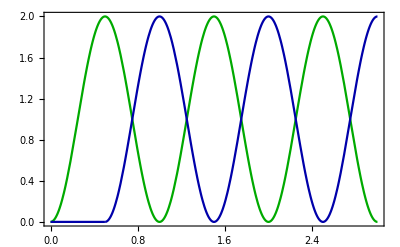

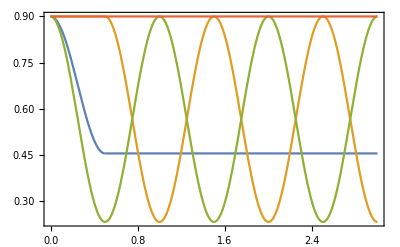

```mathematica
P=1;ΔtA = 0; ΔtB=0.5;
CA[t_]:=Piecewise[{{0,t≤ΔtA},{ Cos[(2Pi (t+P/2-ΔtA))/P]+1,t>ΔtA}}]; 
CB[t_]:=Piecewise[{{0,t≤ΔtB},{Cos[(2Pi (t+P/2-ΔtB))/P]+1,t>ΔtB}}];
μA= 1 10^-3;
μB= 1 10^-4;
dS[t_]:=0.1;
dA[t_]:=0.1; 
dB[t_]:=0.1;
dD[t_]:=0.1; 
αA=1/3; αB = 1/3;
bS[t_]:=1.0 - 2  αA αB(CA[t] + CB[t]); 
bA[t_]:=1.0 - αB CB[t]; 
bB[t_]:=1.0 -αA CA[t];
bD[t_]:=1.0; 
n0 = 10^4;
tmax=100;
Plot[{CA[t],CB[t]},{t,0,3}, PlotStyle->{Darker[Green],Darker[Blue]},BaseStyle->{FontFamily -> "Latin Modern Roman",FontSize->15},Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["\\text{time(a.u.)}", Magnification->1.5],MaTeX["C \\text{(a.u.)}",Magnification->1.5]},PlotLegends->Placed[LineLegend[{MaTeX["C_A", Magnification->1.2],MaTeX["C_B", Magnification->1.2]},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.88,0.79}]]

Plot[{bS[t]-dS[t],bA[t]-dA[t],bB[t]-dB[t],bD[t]-dD[t]},{t,0,3}, BaseStyle->{FontFamily -> "Latin Modern Roman",FontSize->15},Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["\\text{time(a.u.)}", Magnification->1.5],MaTeX["\\text{growth rates}", Magnification->1.5]},PlotLegends->Placed[LineLegend[{MaTeX["r_S", Magnification->1.2],MaTeX["r_A", Magnification->1.2],MaTeX["r_B", Magnification->1.2],MaTeX["r_D", Magnification->1.2]},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.89,0.61}]]
```

#### Pulsing rates

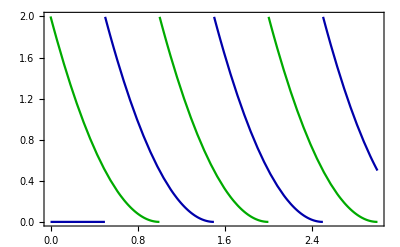

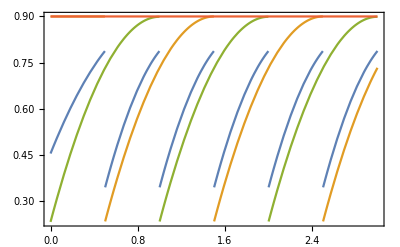

```mathematica
P=1;I0 = 0; I1 = 2.0;ΔtA=0.0; ΔtB = 0.5;
CA0[t_]:=(I1-I0)/P^2(t-ΔtA-P)^2+I0; CA[t_]:=Piecewise[{{0,t≤ΔtA},{ CA0[Mod[t-ΔtA,P]+ΔtA],t>ΔtA}}]; 
CB0[t_]:=(I1-I0)/P^2(t-ΔtB-P)^2+I0; CB[t_]:=Piecewise[{{0,t≤ΔtB},{ CB0[Mod[t-ΔtB,P]+ΔtB],t>ΔtB}}]; 
αA=1/3; αB = 1/3;
bS[t_]:=1.0 - 2  αA αB(CA[t] + CB[t]); 
bA[t_]:=1.0 - αB CB[t]; 
bB[t_]:=1.0 -αA CA[t];
bD[t_]:=1;
μA= 1 10^-3;
μB= 1 10^-4;
dS[t_]:=0.1;
dA[t_]:=0.1; 
dB[t_]:=0.1;
dD[t_]:=0.1; 
n0 = 10^4;
tmax=100;
Plot[{CA[t],CB[t]},{t,0,3}, PlotStyle->{Darker[Green],Darker[Blue]},BaseStyle->{FontFamily -> "Latin Modern Roman",FontSize->15},Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["\\text{time(a.u.)}", Magnification->1.5],MaTeX["C \\text{(a.u.)}",Magnification->1.5]},PlotLegends->Placed[LineLegend[{MaTeX["C_A", Magnification->1.2],MaTeX["C_B", Magnification->1.2]},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.88,0.79}]]
Plot[{bS[t](1-μA-μB)-dS[t],bA[t](1-μB)-dA[t],bB[t](1-μA)-dB[t],bD[t]-dD[t]},{t,0,3}, BaseStyle->{FontFamily -> "Latin Modern Roman",FontSize->15},Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["\\text{time(a.u.)}", Magnification->1.5],MaTeX["\\text{growth rates}", Magnification->1.5]},PlotLegends->Placed[LineLegend[{MaTeX["r_S", Magnification->1.2],MaTeX["r_A", Magnification->1.2],MaTeX["r_B", Magnification->1.2],MaTeX["r_D", Magnification->1.2]},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.89,0.61}]]
```

### Mean values

```mathematica
nsol=NDSolve[{nSe'[t]==(bS[t](1-μA-μB)-dS[t])nSe[t],nAe'[t]==(bA[t](1-μB)-dA[t])nAe[t]+bS[t]μA nSe[t],nBe'[t]==(bB[t](1-μA)-dB[t])nBe[t]+bS[t]μB nSe[t],nDe'[t]==(bD[t]-dD[t])nDe[t]+bA[t]μB nAe[t] + bB[t]μA nBe[t],nSe[0]==n0,nAe[0]==0,nBe[0]==0,nDe[0]==0} ,{nSe,nAe,nBe,nDe},{t,0,tmax},Method->{"DiscontinuityProcessing"->False}];
{nS, nA,nB,nD}=nsol[[1,All,2]];
```

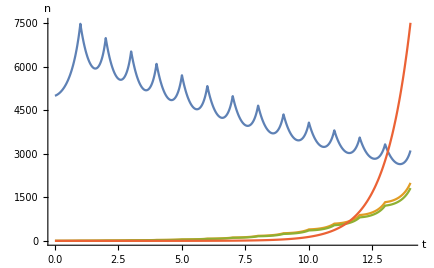

```mathematica
Plot[{nS[t],nA[t],nB[t],nD[t]},{t,0,14},PlotRange->All,AxesLabel->{"t","n"}]
```

### P_ext

```mathematica
nsolext=NDSolve[{nSex'[t]==(bS[t](1-μA-μB)-dS[t])nSex[t],nAex'[t]==(bA[t](1-μB)-dA[t])nAex[t],nBex'[t]==(bB[t](1-μA)-dB[t])nBex[t],nDex'[t]==(bD[t]-dD[t])nDex[t],nSex[0]==1,nAex[0]==1,nBex[0]==1,nDex[0]==1} ,{nSex,nAex,nBex,nDex},{t,0,tmax}];
{nS0, nA0,nB0,nD0}=nsolext[[1,All,2]];
```

```mathematica
nAp[t_ ?NumericQ,tp_ ?NumericQ]:=nA0[tp]/nA0[t];nBp[t_ ?NumericQ,tp_ ?NumericQ]:=nB0[tp]/nB0[t];
nDp[t_ ?NumericQ,tp_ ?NumericQ]:=nD0[tp]/nD0[t];
```

```mathematica
PeFA[t_?NumericQ,T_?NumericQ] := NIntegrate[dA[tp]/nAp[t,tp],{tp,t,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
PeFB[t_?NumericQ,T_?NumericQ] := NIntegrate[dB[tp]/nBp[t,tp],{tp,t,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
PeFD[t_?NumericQ,T_?NumericQ] := NIntegrate[dD[tp]/nDp[t,tp],{tp,t,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
```

```mathematica
betaA[t_?NumericQ,tp_?NumericQ] := NIntegrate[bA[tpp]-dA[tpp],{tpp,t,tp},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
betaB[t_?NumericQ,tp_?NumericQ] := NIntegrate[bB[tpp]-dB[tpp],{tpp,t,tp},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
PeFA[t_?NumericQ,T_?NumericQ] := NIntegrate[dA[tp] Exp[-betaA[t,tp]],{tp,t,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
PeFB[t_?NumericQ,T_?NumericQ] := NIntegrate[dB[tp] Exp[-betaB[t,tp]],{tp,t,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
```

```mathematica
PextA[t_,T_]:=PeFA[t,T]/(1 + PeFA[t,T]);PextB[t_,T_]:=PeFB[t,T]/(1 + PeFB[t,T]);PextD[t_,T_]:=PeFD[t,T]/(1 + PeFD[t,T]);
```

### Probability of single resistance

```mathematica
WA[t_]:=nS[t]bS[t]μA;
WB[t_]:=nS[t]bS[t]μB;
```

```mathematica
PRSingle[T_]:=PRSingle[T]=1-Exp[NIntegrate[WA[t](PextA[t,T] - 1) + WB[t](PextB[t,T] - 1),{t,0,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}, PrecisionGoal->2]];
```

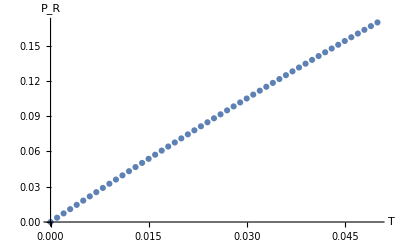

```mathematica
ListPlot[Table[{T,PRSingle[T]},{T,0,0.05, 0.001}],AxesLabel->{"T","P_R"}]
```

### Probability of double resistance

```mathematica
Clear[PRDouble]
```

```mathematica
WD[t_]:=nA[t]bA[t]μB + nB[t]bB[t]μA;
```

```mathematica
PRDouble[T_]:=PRDouble[T]=1-Exp[NIntegrate[WD[t]*(PextD[t,T] - 1),{t,0,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}]];
```

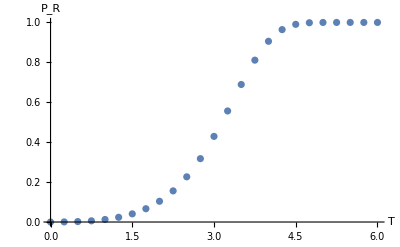

```mathematica
ListPlot[Table[{T,Quiet[PRDouble[T]]},{T,0,6, 0.25}],PlotRange->All,AxesLabel->{"T","P_R"}]
```